# k-means++ Clustering

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Part 1: k-means Animation

If we e.g. start with
-Graphics-
we end up with something like
-Graphics-
which is not really a good clustering result since the two clusters in the bottom end up in one cluster.

The problem is that the distance of the bottom point clouds is smaller to the green cluster centre than to one of the top ones. So, we are already in a local minima and further iterations won’t improve anything. This means that we are stuck with this bad result solely because of the bad initialization.

## Part 2: k-means++ Algorithm

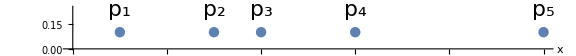

```mathematica
data={1,3,4,6,10};
dataLabels=Subscript[it["p"],#]&/@Range[Length[data]];
ListPlot[MapThread[Callout[{#1,0.1},#2,Top]&,{data,dataLabels}],
PlotTheme->"myTheme",
AspectRatio->1/10,
PlotRange->{Automatic,{0,0.25}},
Axes->{True,False},
AxesLabel->{x},
Ticks->{Range[0,10],Automatic}
]
```

```mathematica
Subscript[c, 1]=data[[2]]
```

3

Distances d_i

```mathematica
distances=DistanceMatrix[{Subscript[c, 1]},data,DistanceFunction->SquaredEuclideanDistance]//Flatten
```

{4,0,1,9,49}

Probabilities P_i

```mathematica
distances/Total[distances]//N
```

{0.0634921,0.,0.015873,0.142857,0.777778}

And the plot of the discrete probability distribution.

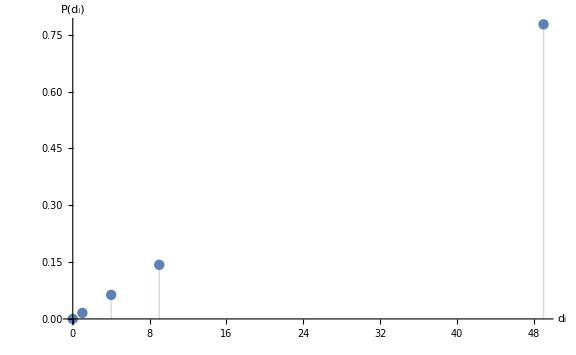

```mathematica
ListPlot[{distances,distances/Total[distances]}ᵀ,
PlotTheme->"myTheme",
PlotRange->All,
AxesLabel->{"d_i","P(d_i)"},
Filling->Axis
]
```

```mathematica
SeedRandom[1337];
Subscript[c, 2]=RandomChoice[distances/Total[distances]->data]
```

10

New distance values.

```mathematica
distances2=MapThread[SquaredEuclideanDistance[#1,#2]&,{Flatten[Nearest[{Subscript[c, 1],Subscript[c, 2]},data],1],data}]
```

{4,0,1,9,0}

And new probability values.

```mathematica
distances2/Total[distances2]
```

{2/7,0,1/14,9/14,0}

The first data point p_1 is selected 4 times, p_2 not at all, p_3 once, p_4 9 times and p_5 again not at all.

## Part 3: Video

https://www.youtube.com/watch?v=BIQDlmZDuf8

There is no guarantee that always the point with the largest distance is chosen and this is also not intended. Points with higher distances just have a higher probability of being chosen.

The argument for this might be that we want the algorithm to be robuster against outliers. If we always chose the point with the largest distance, we might end up selecting one outlier after another (outliers tend to be far away).